```mathematica
Kernel
```

```mathematica
WeightedKernel[x_,y_,xi_,yi_,s_]:=1/(Sqrt[Pi]* s)*Exp[-((x-xi)^2 + (y-yi)^2)/s^2];
```

```mathematica
Gradients
```

```mathematica
RA[x_]:=Exp[x-0.5];
LA[x_]:=Exp[-x+0.5];
RB[x_]:=Exp[x-0.5];
LB[x_]:=Exp[-x+0.5];
EphA3[x_]:=Exp[-(x-xa3)^2/s^2]
```

General::munfl: Exp[-3999.18] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-15998.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-35997.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

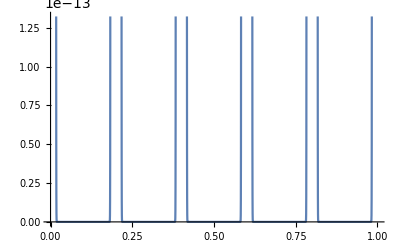

```mathematica
Plot[EphA3[x],{x,0,1}]
```

```mathematica
Activity
```

```mathematica
Ca[xi_,yi_,xj_,yj_,σ_]:=Exp[-((xi-xj)^2+(yi-yj)^2)/(2*σ^2)]
```

```mathematica
Energies
```

The competition energy for a given retinal index ‘i’ is the self-convolution of the second derivative evaluated at the origin.

```mathematica
Ecompij=D[D[Integrate[WeightedKernel[x-w,y-t,xi,yi,s]*WeightedKernel[w,t,xj,yj,s],{w,0,1},{t,0,1}],x],y]/.{x->0,y->0};
Ecompijsimple=Integrate[WeightedKernel[x,y,xi,yi,s]*WeightedKernel[x,y,xj,yj,s],{x,0,1},{y,0,1}]
Ecompijtotal=Integrate[WeightedKernel[x,y,xi,yi,s]*WeightedKernel[x,y,xj,yj,s],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1/8 ⅇ^(-((xi-xj)^2+(yi-yj)^2)/(2 s^2)) (Erf[(-2+xi+xj)/(√2 s)]-Erf[(xi+xj)/(√2 s)]) (Erf[(-2+yi+yj)/(√2 s)]-Erf[(yi+yj)/(√2 s)])

ConditionalExpression[1/2 ⅇ^(-((xi-xj)^2+(yi-yj)^2)/(2 s^2)), Re[s^2]≥0]

The competition energy can also be evaluated directly:

The activity energy for an index pair is straightforward:

```mathematica
Eactij=Integrate[WeightedKernel[w,t,xi,yi,s]*WeightedKernel[w,t,xj,yj,s]*Ca[xi,yi,xj,yj,σcol]*Ca[xreti,yreti,xretj,yretj,σret],{w,0,1},{t,0,1}]
Eactijtotal = Integrate[WeightedKernel[w,t,xi,yi,s]*WeightedKernel[w,t,xj,yj,s]*Ca[xi,yi,xj,yj,σcol]*Ca[xreti,yreti,xretj,yretj,σret],{w,-Infinity,Infinity},{t,-Infinity,Infinity}]
```

(ⅇ^(1/2 (-(xi^2-2 xi xj+xj^2+(yi-yj)^2)/s^2-(xreti^2 σcol^2-2 xreti xretj σcol^2+xretj^2 σcol^2+yreti^2 σcol^2-2 yreti yretj σcol^2+yretj^2 σcol^2+xi^2 σret^2-2 xi xj σret^2+xj^2 σret^2+yi^2 σret^2-2 yi yj σret^2+yj^2 σret^2)/(σcol^2 σret^2))) (Erf[(-2+xi+xj)/(√2 s)]-Erf[(xi+xj)/(√2 s)]) ((-2+yi+yj) √((yi+yj)^2/s^2) Erf[(√((-2+yi+yj)^2/s^2))/(√2)]-√((-2+yi+yj)^2/s^2) (yi+yj) Erf[(√((yi+yj)^2/s^2))/(√2)]))/(8 s √((-2+yi+yj)^2/s^2) √((yi+yj)^2/s^2))

The chemical energy is even more straightforward

```mathematica
Echemi=Integrate[WeightedKernel[w,t,xi,yi,s]*(α*(RA[xret]*LA[w]-RA[w]*LA[xret])+β*(RB[yret]*LB[t]-RB[t]*LB[yret])),{w,0,1},{t,0,1}]
EchemiephrinA2A5=Integrate[WeightedKernel[w,t,xi,yi,s]*(α*(RA[xret]*LA[w])+β*(RB[yret]*LB[t]-RB[t]*LB[yret])),{w,0,1},{t,0,1}]
EchemiEphA3=Integrate[WeightedKernel[w,t,xi,yi,s]*(α*((RA[xret]+EphA3[xret])*LA[w]-RA[w]*LA[xret])+β*(RB[yret]*LB[t]-RB[t]*LB[yret])),{w,0,1},{t,0,1}]
(*Echemitotal=Integrate[WeightedKernel[w,t,xi,yi,s]*(α*(RA[xret]*LA[w]-RA[w]*LA[xret])+β*(RB[yret]*LB[t]-RB[t]*LB[yret])),{w,-Infinity,Infinity},{t,-Infinity,Infinity}]*)
```

1/4 ⅇ^(s^2/4) √π s (ⅇ^(-xi-xret) α (ⅇ^(2 xret) (Erf[(2+s^2-2 xi)/(2 s)]-Erf[s/2-xi/s])+ⅇ^(2 xi) (Erf[(-2+s^2+2 xi)/(2 s)]-Erf[s/2+xi/s])) (Erf[(1-yi)/s]+Erf[yi/s])+ⅇ^(-yi+yret) β (Erf[(1-xi)/s]+Erf[xi/s]) (Erf[(2+s^2-2 yi)/(2 s)]-Erf[s/2-yi/s])+ⅇ^(yi-yret) β (Erf[(1-xi)/s]+Erf[xi/s]) (Erf[(-2+s^2+2 yi)/(2 s)]-Erf[s/2+yi/s]))

1/4 ⅇ^(s^2/4) √π s (ⅇ^(-xi+xret) α (Erf[(2+s^2-2 xi)/(2 s)]-Erf[s/2-xi/s]) (Erf[(1-yi)/s]+Erf[yi/s])+ⅇ^(-yi-yret) β (Erf[(1-xi)/s]+Erf[xi/s]) (ⅇ^(2 yret) (Erf[(2+s^2-2 yi)/(2 s)]-Erf[s/2-yi/s])+ⅇ^(2 yi) (Erf[(-2+s^2+2 yi)/(2 s)]-Erf[s/2+yi/s])))

1/2 ⅇ^(0.25 s^2) s (ⅇ^(-1. xi-1. xret) α (ⅇ^(2. xi) Erf[(0.5 (-2.+s^2+2. xi))/s] (0.886227 Erf[(1-yi)/s]+0.886227 Erf[yi/s])+ⅇ^((-1. xa3^2-1. xret^2)/s^2) (1.46114 ⅇ^((1.+(2. xa3)/s^2) xret)+0.886227 ⅇ^(2. xret+(1. xa3^2+1. xret^2)/s^2)) Erf[(0.5 (2.+s^2-2. xi))/s] (Erf[(1.-1. yi)/s]+Erf[yi/s]))-ⅇ^(-1. xi-1. xret) α (ⅇ^(2. xi) Erf[0.+0.5 s+(1. xi)/s] (0.886227 Erf[(1-yi)/s]+0.886227 Erf[yi/s])+ⅇ^((-1. xa3^2-1. xret^2)/s^2) (1.46114 ⅇ^((1.+(2. xa3)/s^2) xret)+0.886227 ⅇ^(2. xret+(1. xa3^2+1. xret^2)/s^2)) Erf[0.+0.5 s-(1. xi)/s] (Erf[(1.-1. yi)/s]+Erf[yi/s]))+0.886227 ⅇ^(-1. yi-1. yret) β Erf[(1-1. xi)/s] (1. ⅇ^(2. yret) Erf[(0.5 (2.+s^2-2. yi))/s]+1. ⅇ^(2. yi) Erf[(0.5 (-2.+s^2+2. yi))/s]-1. ⅇ^(2. yret) Erf[0.5 s-(1. yi)/s]-1. ⅇ^(2. yi) Erf[0.5 s+yi/s])+0.886227 ⅇ^(-1. yi-1. yret) β Erf[(1. xi)/s] (1. ⅇ^(2. yret) Erf[(0.5 (2.+s^2-2. yi))/s]+1. ⅇ^(2. yi) Erf[(0.5 (-2.+s^2+2. yi))/s]-1. ⅇ^(2. yret) Erf[0.5 s-(1. yi)/s]-1. ⅇ^(2. yi) Erf[0.5 s+yi/s]))

Try the mass action law as the gradient itself

```mathematica
Echemi=Integrate[Integrate[Integrate[WeightedKernel[w,t,xi,yi,s]*(α*(RA[xret]*LA[w]-RA[w]*LA[xret])+β*(RB[yret]*LB[t]-RB[t]*LB[yret])),{w,0,1},{t,0,1}],xi],yi]
```

Doing some simplifications.

```mathematica
FullSimplify[Ecompijsimple,Assumptions->{xi>0,yi>0,s>0,xj>0,yj>0}]
```

1/8 ⅇ^(-((xi-xj)^2+(yi-yj)^2)/(2 s^2)) (Erf[(-2+xi+xj)/(√2 s)]-Erf[(xi+xj)/(√2 s)]) (Erf[(-2+yi+yj)/(√2 s)]-Erf[(yi+yj)/(√2 s)])

```mathematica
FullSimplify[Eactij,Assumptions->{xi>0,yi>0,s>0,xj>0,yj>0}]
```

1/8 ⅇ^(1/2 (-(((xi-xj)^2+(yi-yj)^2) (s^2+σcol^2))/(s^2 σcol^2)-((xreti-xretj)^2+(yreti-yretj)^2)/σret^2)) (Erf[(-2+xi+xj)/(√2 s)]-Erf[(xi+xj)/(√2 s)]) (Erf[(-2+yi+yj)/(√2 s)]-Erf[(yi+yj)/(√2 s)])

```mathematica
FullSimplify[Echemi,Assumptions->{xi>0,yi>0,s>0,xj>0,yj>0}]
FullSimplify[EchemiephrinA2A5,Assumptions->{xi>0,yi>0,s>0,xj>0,yj>0}]
FullSimplify[EchemiEphA3,Assumptions->{xi>0,yi>0,s>0,xj>0,yj>0}]
```

1/4 ⅇ^(s^2/4) √π s (ⅇ^(-xi-xret) α (ⅇ^(2 xret) (Erf[(2+s^2-2 xi)/(2 s)]-Erf[s/2-xi/s])+ⅇ^(2 xi) (Erf[(-2+s^2+2 xi)/(2 s)]-Erf[s/2+xi/s])) (Erf[(1-yi)/s]+Erf[yi/s])+ⅇ^(-yi+yret) β (Erf[(1-xi)/s]+Erf[xi/s]) (Erf[(2+s^2-2 yi)/(2 s)]-Erf[s/2-yi/s])+ⅇ^(yi-yret) β (Erf[(1-xi)/s]+Erf[xi/s]) (Erf[(-2+s^2+2 yi)/(2 s)]-Erf[s/2+yi/s]))

1/4 ⅇ^(s^2/4) √π s (ⅇ^(-xi+xret) α (Erf[(2+s^2-2 xi)/(2 s)]-Erf[s/2-xi/s]) (Erf[(1-yi)/s]+Erf[yi/s])+ⅇ^(-yi-yret) β (Erf[(1-xi)/s]+Erf[xi/s]) (ⅇ^(2 yret) (Erf[(2+s^2-2 yi)/(2 s)]-Erf[s/2-yi/s])+ⅇ^(2 yi) (Erf[(-2+s^2+2 yi)/(2 s)]-Erf[s/2+yi/s])))

```mathematica
x
```

The total energy for a retinal neurone ‘i’ is then the chemical energy terms plus the sum over all j over the activity and competitive terms. We just need to assemble them.

```mathematica
Manipulate[Plot[Out[106]^2,{xi,-1,1}],{xret,0,1},{yret,0,1},{yi,0,1},{s,0.001,1},{β,0,1},{α,0,1}]
```

```mathematica
Manipulate[Plot[-RA[x]*LA[xu]-RA[xu]*LA[x],{x,0,1}],{xu,0,1}]
```

```mathematica
Integrate[RA[x]*LA[xu]-RA[xu]*LA[x],xu]
```

-ⅇ^(x-xu)-ⅇ^(-x+xu)

```mathematica
-RA[x]*LA[xu]-RA[xu]*LA[x]
```

-ⅇ^(0.+x-xu)-ⅇ^(0.-x+xu)